# Wilberforce Pendulum modelling PHYS1201 ASE project, 2022

## By Campbell McTernan and Aditya Singh Tejas

## Introduction

This project requires the creation and investigation of a complex mechanical system as least as complex as a double pendulum. For this task, we have chosen the Wilberforce pendulum which was first described by the physicist Lionel Robert Wilberforce  in 1896. The Wilberforce pendulum is constructed by hanging  a mass which is free to rotate in the direction of the coils, with certain harmonic properties which allow for energy to alternate between purely vertical and rotational motion. This is achieved through a coupling of the rotational and spring potential energy of the system. 

This investigation focuses on the description and analysis of the pendulum, using the Euler-Lagrange equations of motion to predict the pendulum’s path, and representing this in Mathematica. This document primarily serves to describe the theoretical implications of design choices for the pendulum and to predict its path using computational software.

## The Wilberforce Pendulum

The mass  is free to slide along a frictionless rail. The Wilberforce pendulum consists of a cylindrical mass  (moment of inertia ) suspended by a helical spring of natural length , longitudinal spring constant  and torsional spring constant . We assume that the spring has negligible mass and is rigid along its axis throughout the experiment. The cylinder must hang such that its axis is always in the plane orthogonal to the direction of the spring, and is free to rotate along this plane. The spring makes an angle  from the vertical and the tracked point on the cylinder creates an angle  from the measured from the starting point in its rotational plane . The horizontal position of the mass  is noted as  from the origin  : see figure. We choose the reference of the gravitational potential energy to be zero at the height of mass . Note that the motion is actually in 3 dimensions but, the z-axis (into the page) is essential irrelevant for the motion of equations, as it can be represented by .


	-Graphics-


Note that there are four coordinates, that is, θ, ,  and . There are four Euler-Lagrange equations and these must be solved simultaneously.

### Deriving the Euler-Lagrange equations

Start by deriving the kinetic and potential energies, and hence the Lagrangian. Although you should formulate the dynamics using the angles, θ_1 and θ_2, it is easier to set it up in Cartesian coordinates:


We will start by considering all aspects of energy in the system to later conclude on the Lagrangian:

Kinetic energy
As the entire system is free to slide along a rail, the system can obtain velocity and thus kinetic energy. Defining  to be the velocity of the system, we thus have  . Furthermore, the cylinder  itself will have velocity relative to the system  and rotational energy dependant on the rotational velocity  given by  and  . 

Thus, the total kinetic energy of the system is  , so



Potential energy

We know that a spring with spring constant  and stretch length  has a spring potential  . We also know that the torsional potential of the spring is . Since these potentials are coupled, we furthermore have the potential  which represents the shared energy held during the transfer of energy between  and  in the system. As there are only two coupled components of potential, this relationship is linear and proportional to  and . Thus, assume  where  is some constant. Finally, as this Wilberforce experiment has been made unique by the inclusion of traditional swinging pendulum motion, we also have gravitational potential  . 

Thus, the total kinetic energy of the system is  , so



Lagrangian

```mathematica
Subscript[x, 0] = x[t]; Subscript[y, 0] = 0;
Subscript[x, 1]=(l+s[t]) Sin[ θ[t]]+ Subscript[x, 0];Subscript[y, 1]=-(l+s[t]) Cos[θ[t]]+Subscript[y, 0];
Subscript[x, 2]=r Cos[α[t]] Cos[ θ[t]]+Subscript[x, 1];Subscript[y, 2]=r Cos[α[t]] Sin[ θ[t]]+Subscript[y, 1];
i = (M r^2)/3
```

(M r^2)/3

The kinetic energy is then:

```mathematica
K=0.5 (m+M) (D[Subscript[x, 0],t]^2)+0.5 M(D[Subscript[x, 1],t]^2+D[Subscript[y, 1],t]^2)+0.5 i ((D[α[t], t])^2)
```

0.5 (m+M) x'[t]^2+0.166667 M r^2 α'[t]^2+0.5 M ((Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (l+s[t]) θ'[t])^2+(-Cos[θ[t]] s'[t]-(-l-s[t]) Sin[θ[t]] θ'[t])^2)

Use FullSimplify to simplify trigonometric terms.

```mathematica
K=FullSimplify[K]
```

0.5 (m+M) x'[t]^2+0.166667 M r^2 α'[t]^2+0.5 M ((Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (l+s[t]) θ'[t])^2+(Cos[θ[t]] s'[t]-(l+s[t]) Sin[θ[t]] θ'[t])^2)

Choose the potential energy zero to be at y_1 = y_2 = 0 :

```mathematica
V=0.5 k s[t]^2 + 0.5 δ α [t]^2 + α[t]ϕ s[t]+ Mg Cos [θ[t]](l + s[t] )
```

0.5 k s[t]^2+Mg Cos[θ[t]] (l+s[t])+ϕ s[t] α[t]+0.5 δ α[t]^2

Use FullSimplify to simplify trigonometric terms.

```mathematica
V=FullSimplify[V]
```

0.5 k s[t]^2+Mg Cos[θ[t]] (l+s[t])+ϕ s[t] α[t]+0.5 δ α[t]^2

The Lagrangian :

```mathematica
L=K-V
```

-0.5 k s[t]^2-Mg Cos[θ[t]] (l+s[t])-ϕ s[t] α[t]-0.5 δ α[t]^2+0.5 (m+M) x'[t]^2+0.166667 M r^2 α'[t]^2+0.5 M ((Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (l+s[t]) θ'[t])^2+(Cos[θ[t]] s'[t]-(l+s[t]) Sin[θ[t]] θ'[t])^2)

Next calculate the derivatives in the Euler-Lagrange equation:

```mathematica
dLdθ=D[L,θ[t]] (* θ derivative *)
```

Mg (l+s[t]) Sin[θ[t]]+0.5 M (2 (-Sin[θ[t]] s'[t]-Cos[θ[t]] (l+s[t]) θ'[t]) (Cos[θ[t]] s'[t]-(l+s[t]) Sin[θ[t]] θ'[t])+2 (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (l+s[t]) θ'[t]) (Cos[θ[t]] s'[t]-(l+s[t]) Sin[θ[t]] θ'[t]))

```mathematica
dLdα=D[L,α[t]] (* α derivative *)
```

-ϕ s[t]-1. δ α[t]

```mathematica
dLds=D[L,s[t]] (* s derivative *)
```

-Mg Cos[θ[t]]-1. k s[t]-ϕ α[t]+0.5 M (2 Cos[θ[t]] θ'[t] (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (l+s[t]) θ'[t])-2 Sin[θ[t]] θ'[t] (Cos[θ[t]] s'[t]-(l+s[t]) Sin[θ[t]] θ'[t]))

```mathematica
dLdx=D[L,x[t]] (* x derivative *)
```

0

```mathematica
dLdashdx=D[L,x'[t]] (* x' derivative *)
```

1. (m+M) x'[t]+1. M (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (l+s[t]) θ'[t])

```mathematica
dLdashds=D[L,s'[t]] (* s' derivative *)
```

0.5 M (2 Sin[θ[t]] (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (l+s[t]) θ'[t])+2 Cos[θ[t]] (Cos[θ[t]] s'[t]-(l+s[t]) Sin[θ[t]] θ'[t]))

```mathematica
dLdashdα=D[L,α'[t]] (* α' derivative *)
```

0.333333 M r^2 α'[t]

```mathematica
dLdashdθ=D[L,θ'[t]] (* θ' derivative *)
```

0.5 M (2 Cos[θ[t]] (l+s[t]) (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (l+s[t]) θ'[t])-2 (l+s[t]) Sin[θ[t]] (Cos[θ[t]] s'[t]-(l+s[t]) Sin[θ[t]] θ'[t]))

Calculate the Euler-Lagrange equation for θ:

```mathematica
ELEθ=0==FullSimplify[dLdθ-D[dLdashdθ,t]]
```

0==-1. M s[t]^2 θ''[t]+s[t] (Mg Sin[θ[t]]-2. M s'[t] θ'[t]-1. M Cos[θ[t]] x''[t]-2. l M θ''[t])+l (Mg Sin[θ[t]]-2. M s'[t] θ'[t]-1. M Cos[θ[t]] x''[t]-1. l M θ''[t])

Calculate the Euler-Lagrange equation for α:

```mathematica
ELEα= 0==FullSimplify[dLdα-D[dLdashdα,t]]
```

0==-ϕ s[t]-1. δ α[t]-0.333333 M r^2 α''[t]

```mathematica
ELEs= 0==FullSimplify[dLds-D[dLdashds,t]]
```

0==-1. Mg Cos[θ[t]]-1. ϕ α[t]+1. l M θ'[t]^2+s[t] (-1. k+1. M θ'[t]^2)-1. M s''[t]-1. M Sin[θ[t]] x''[t]

```mathematica
ELEx= 0==FullSimplify[dLdx-D[dLdashdx,t]]
```

0==-1. (m+M) x''[t]-1. M (Sin[θ[t]] (-((l+s[t]) θ'[t]^2)+s''[t])+x''[t]+Cos[θ[t]] (2 s'[t] θ'[t]+(l+s[t]) θ''[t]))

### Numerically solving the Euler-Lagrange equations

Choose the parameters.

```mathematica
m=0.002;M=0.3; g=9.8;l=0.3;r=0.05; ϕ = 0.3;
```

Solve the Euler-Lagrange equations:

```mathematica
solndp=NDSolve[{ELEθ,ELEα,ELEs,ELEx,θ[0]==Pi/2,α[0]==0,θ'[0]==0,α'[0]==0, s[0] == 0, s'[0] == 0, x[0] == 0, x'[0] == 0},{θ,α, s, x},{t,0,10}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{0==s[t] (Mg Sin[θ[t]]-0.6 s'[t] θ'[t]-0.3 Cos[θ[t]] x''[t]-0.18 θ''[t])+0.3 (Mg Sin[θ[t]]-0.6 s'[t] θ'[t]-0.3 Cos[θ[t]] x''[t]-0.09 θ''[t])-0.3 s[t]^2 θ''[t],0==-0.3 s[t]-1. δ α[t]-0.00025 α''[t],0==-1. Mg Cos[θ[t]]-0.3 α[t]+0.09 θ'[t]^2+s[t] (-1. k+0.3 θ'[t]^2)-0.3 s''[t]-0.3 Sin[θ[t]] x''[t],0==-0.302 x''[t]-0.3 (Sin[θ[t]] (-((0.3+s[t]) θ'[t]^2)+s''[t])+x''[t]+Cos[θ[t]] (2 s'[t] θ'[t]+(0.3+s[t]) θ''[t])),θ[0]==π/2,α[0]==0,θ'[0]==0,α'[0]==0,s[0]==0,s'[0]==0,x[0]==0,x'[0]==0},{θ,α,s,x},{t,0,10}]

```mathematica
|
```

```mathematica
|
```

Plot y_1 and y_2 coordinates vs time. Include a title for the plot and axes labels with units.

```mathematica
Plot[Evaluate[{Subscript[y, 1],Subscript[y, 2]}/.solndp],{t,0,10},PlotRange->All,AxesLabel->{"t (s)","y, y (m)"},PlotLabel->"y_1 and y vs time."]
```

ReplaceAll::reps: {NDSolve[{0==s[t] (Times[«2»]+Times[«3»]+Times[«3»]+Times[«2»])+0.3 (Times[«2»]+Times[«3»]+Times[«3»]+Times[«2»])-0.3 s[«1»]^2 θ''[t],α==-1. δ α[t]-1. i α''[t],s==-1. Mg Cos[θ[«1»]]-1. ϕα[t]+0.09 ((«1»)^(«1»)[«1»])^2+s[t] (Times[«2»]+Times[«2»])-0.3 s''[t]-0.3 Sin[θ[«1»]] x''[t],x==0,θ[0]==π/2,α[0]==0,θ'[0]==0,α'[0]==0,0,0,«2»},{θ,α,s,x},{t,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0==s[0.000204286] (Times[«2»]+Times[«3»]+Times[«3»]+Times[«2»])+0.3 (Times[«2»]+Times[«3»]+Times[«3»]+Times[«2»])-0.3 s[«1»]^2 θ''[0.000204286],α==-1. δ α[0.000204286]-1. i α''[0.000204286],«7»,0,«2»},{θ,α,s,x},{0.000204286,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==s[0.000204286] (Times[«2»]+Times[«3»]+Times[«3»]+Times[«2»])+0.3 (Times[«2»]+Times[«3»]+Times[«3»]+Times[«2»])-0.3 s[«1»]^2 θ''[0.000204286],α==-1. δ α[0.000204286]-1. i α''[0.000204286],«7»,0.,«2»},{θ,α,s,x},{0.000204286,0.,10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

Plot trajectories in x, y plane.

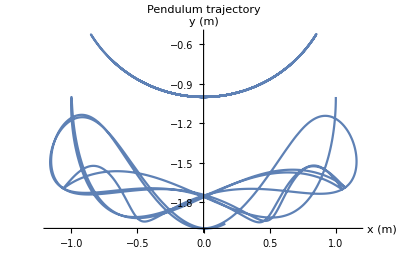

```mathematica
ParametricPlot[{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solndp,{t,0,10},PlotRange->All,AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory"]
```

Animate trajectories in x, y plane.

```mathematica
Animate[ParametricPlot[{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solndp,{t,0,tend},PlotRange->{{-1.5,1.5},{-2.5,0}},AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory"],{tend,0,10},AnimationRepetitions->3]
```

### Adding damping

We add terms proportional to the angular velocities θ_1' and θ_2' with the same proportionality constant α.

Damped dynamical equations:

```mathematica
ELEθoneDamped=0==FullSimplify[D[Subscript[dLdashdθ, 1],t]-Subscript[dLdθ, 1] +α Subscript[θ, 1]'[t]]
```

0==19.6 Sin[θ_1[t]]+1. α θ_1'[t]+1. Sin[θ_1[t]-θ_2[t]] θ_2'[t]^2+2. θ_1''[t]+1. Cos[θ_1[t]-θ_2[t]] θ_2''[t]

```mathematica
ELEθtwoDamped=0==FullSimplify[D[Subscript[dLdashdθ, 2],t]-Subscript[dLdθ, 2] +α Subscript[θ, 2]'[t]]
```

0==9.8 Sin[θ_2[t]]-1. Sin[θ_1[t]-θ_2[t]] θ_1'[t]^2+1. α θ_2'[t]+1. Cos[θ_1[t]-θ_2[t]] θ_1''[t]+1. θ_2''[t]

Choose the damping parameter and solve the Euler-Lagrange equation:

```mathematica
α=0.01; soln=NDSolve[{ELEθoneDamped,ELEθtwoDamped, Subscript[θ, 1][0]==0,Subscript[θ, 2][0]==Pi/2,Subscript[θ, 1]'[0]==0,Subscript[θ, 2]'[0]==0},{Subscript[θ, 1],Subscript[θ, 2]},{t,0,10}]
```

{{θ_1→InterpolatingFunction[{{0., 10.}}, <>],θ_2→InterpolatingFunction[{{0., 10.}}, <>]}}

Plot y_1 and y_2 coordinates vs time. Include a title for the plot and axes labels with units.

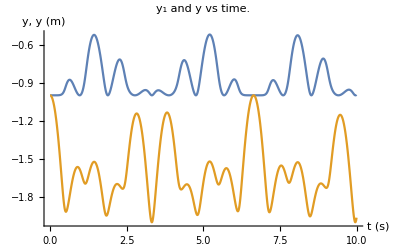

```mathematica
Plot[Evaluate[{Subscript[y, 1],Subscript[y, 2]}/.solndp],{t,0,10},PlotRange->All,AxesLabel->{"t (s)","y, y (m)"},PlotLabel->"y_1 and y vs time."]
```

```mathematica
Clear["Global`*"]
```